The workspace for the derivation of the transformation angle for coupled two level systems

Hamiltonian with corresponding eigenvalues and eigenvectors

```mathematica
Eigenvalues[{{Subscript[ϵ, a],V},{V,Subscript[ϵ, b]}}]//FullSimplify
```

{1/2 (ϵ_a-√(4 V^2+(ϵ_a-ϵ_b)^2)+ϵ_b),1/2 (ϵ_a+√(4 V^2+(ϵ_a-ϵ_b)^2)+ϵ_b)}

```mathematica
Eigenvectors[{{Subscript[ϵ, a],V},{V,Subscript[ϵ, b]}}]//FullSimplify
```

{{-(-ϵ_a+√(4 V^2+(ϵ_a-ϵ_b)^2)+ϵ_b)/(2 V),1},{(ϵ_a+√(4 V^2+(ϵ_a-ϵ_b)^2)-ϵ_b)/(2 V),1}}

Apply rotation matrix to the eigenvector

```mathematica
{-(-Subscript[ϵ, a]+√(4 V^2+(Subscript[ϵ, a]-Subscript[ϵ, b])^2)+Subscript[ϵ, b])/(2 V),1}.{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}//FullSimplify
```

{-Sin[θ]-(Cos[θ] (-ϵ_a+√(4 V^2+(ϵ_a-ϵ_b)^2)+ϵ_b))/(2 V),Cos[θ]-(Sin[θ] (-ϵ_a+√(4 V^2+(ϵ_a-ϵ_b)^2)+ϵ_b))/(2 V)}

Solving one of the components between the two eigenvectors to obtain the transformation angle θ

```mathematica
Reduce[Cos[θ]-(Sin[θ] (-Subscript[ϵ, a]+√(4 V^2+(Subscript[ϵ, a]-Subscript[ϵ, b])^2)+Subscript[ϵ, b]))/(2 V)==1,θ]
```

C[1]∈ℤ&&V≠0&&(θ==2 π C[1]||(4 V^2+ϵ_a^2-2 ϵ_a ϵ_b+ϵ_b^2-ϵ_a √(4 V^2+ϵ_a^2-2 ϵ_a ϵ_b+ϵ_b^2)+ϵ_b √(4 V^2+ϵ_a^2-2 ϵ_a ϵ_b+ϵ_b^2)≠0&&θ==2 ArcTan[(ϵ_a-ϵ_b-√(4 V^2+ϵ_a^2-2 ϵ_a ϵ_b+ϵ_b^2))/(2 V)]+2 π C[1]))

Based on the boundary conditions above, 0 < θ < π/2 and have θ in the form

```mathematica
Tan[2θ]==(2V)/(Subscript[ϵ, a]-Subscript[ϵ, b]);
```

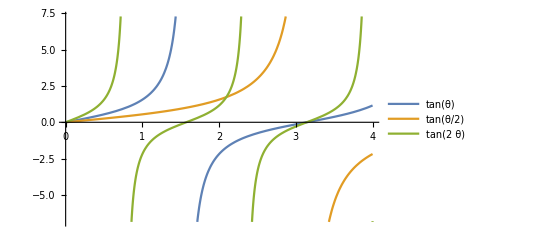

```mathematica
Plot[{Tan[θ],Tan[θ/2],Tan[2θ]},{θ,0,4},PlotLegends->"Expressions"]
```

Time evolution operator in the basis of ϕ_a and ϕ_b

```mathematica
U[t_,t0_,θ_,χ_,h_]:={{Cos[θ]^2,Exp[-I χ]Sin[θ]Cos[θ]},
{Exp[I χ]Sin[θ]Cos[θ],Sin[θ]^2}}Exp[-I/h SubPlus[ϵ](t-t0)]+{{Cos[θ]^2,-Exp[-I χ]Sin[θ]Cos[θ]},
{-Exp[I χ]Sin[θ]Cos[θ],Sin[θ]^2}}Exp[-I/h SubMinus[ϵ](t-t0)]
```

Determining the probability of the system in ϕ_a at a given time t

```mathematica
{0,1}.U[t,0,θ,χ,h].{1,0}
```

-ⅇ^(ⅈ χ-(ⅈ t ϵ_-)/h) Cos[θ] Sin[θ]+ⅇ^(ⅈ χ-(ⅈ t ϵ_+)/h) Cos[θ] Sin[θ]

```mathematica
(-ⅇ^(ⅈ χ)(Cos[(t SubMinus[ϵ])/h]-ⅈ Sin[(t SubMinus[ϵ])/h]) Cos[θ] Sin[θ]+ⅇ^(ⅈ χ)(Cos[(t SubPlus[ϵ])/h]-ⅈ Sin[(t SubPlus[ϵ])/h]) Cos[θ] Sin[θ])*(-ⅇ^(-ⅈ χ)(Cos[(t SubMinus[ϵ])/h]+ⅈ Sin[(t SubMinus[ϵ])/h]) Cos[θ] Sin[θ]+ⅇ^(-ⅈ χ)(Cos[(t SubPlus[ϵ])/h]+ⅈ Sin[(t SubPlus[ϵ])/h]) Cos[θ] Sin[θ])//FullSimplify
```

Sin[2 θ]^2 Sin[(t (ϵ_--ϵ_+))/(2 h)]^2

```mathematica
probAB[v_,ea_,eb_,h_,t_]:=(4 v^2)/(4 v^2+(ea-eb)^2)Sin[Sqrt[4v+(ea-eb)^2]/(2h)t]
```

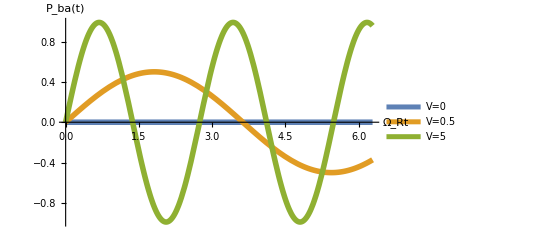

```mathematica
prob2sys=Plot[{probAB[0,0,1,1,t],probAB[0.5,0,1,1,t],probAB[5,0,1,1,t]},{t,0,2Pi},AxesLabel->{"Ω_Rt","P_ba(t)"},PlotLegends->{"V=0","V=0.5","V=5"},
PlotStyle->{Thickness[0.01]},TicksStyle->Directive[14],LabelStyle-> Directive[14]]
```

```mathematica
Export["prob2.eps",prob2sys]
```

prob2.eps